# POE Lab 2 - 3D Scanner

## Voltage to Distance

```mathematica
distanceCSV=Import["https://raw.githubusercontent.com/HALtheWise/POE-lab2/master/docs/zeroPassDistances.csv","Csv"];
distanceData=distanceCSV[[2;;Length[distanceCSV]-1]];
```

```mathematica
Fit[Map[Reverse,distanceData], {1,x,x^2,x^3},x]
```

230.143-1.4452 x+0.00354446 x^2-2.93605×10^-6 x^3

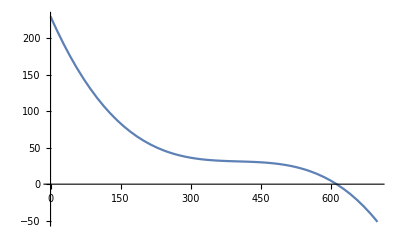

```mathematica
Plot[230.1430411867322-1.4451995839029892 x+0.0035444572391777783 x^2-2.9360497052173657*^-6 x^3,{x,0,700}]
```

## Make Functions voltageToDistance anglesToPan anglesToTilt panTiltDistance sphericalToCartesian-not sure if working correctly

```mathematica
voltageToDistance[x_]=(230.1430411867322-1.4451995839029892 x+0.0035444572391777783 x^2-2.9360497052173657*^-6 x^3);
anglesToPan[servo1_,servo2_]:=Module[{},(N@servo1-servo2)/2]
anglesToTilt[servo1_,servo2_]:=Module[{},(N@servo1+servo2)/2]
```

```mathematica
panTiltDistance[{servo1_,servo2_,voltage_}]:=Module[{pan,tilt,distance},
pan=anglesToPan[servo1,servo2];
tilt=anglesToTilt[servo1,servo2];
distance=voltageToDistance[voltage];
Return[{distance,tilt,pan}]
]
```

```mathematica
toCartesian[{distance_,tilt_,pan_}]:=Module[{radPan,radTilt},
radPan=pan*π/180;
radTilt=pan*π/180;
{distance Cos[radPan] Sin[radTilt],distance Cos[radTilt] Cos[radPan],distance Sin[tilt]}
]
```

## Open Serial device and start reading data

```mathematica
points={};
```

```mathematica
serial=DeviceOpen["Serial",{"/dev/ttyUSB0","BaudRate"->19200}]
```

DeviceObject[…]

```mathematica
Dynamic@ListPointPlot3D[AppendTo[points,toCartesian[panTiltDistance[ToExpression[StringSplit[FromCharacterCode[DeviceReadBuffer[serial,"ReadTerminator"->10]],","]]]]],ImageSize->Large]
```

## Close serial device

```mathematica
DeviceClose[serial]
```